# Mathematical Methods Using Mathematica : For Student of Physics and Related Fields

1.7. An Example from Optics

```mathematica
amp[N_, phi_] :=Sum[E^(I k phi),{k, 0, N-1}]
```

```mathematica
amp[N,ϕ]
```

(-1+ⅇ^(ⅈ N ϕ))/(-1+ⅇ^(ⅈ ϕ))

```mathematica
num1[N_,phi_]=ComplexExpand[Numerator[amp[N, ϕ]]]
```

ⅈ sin(N ϕ)+cos(N ϕ)-1

```mathematica
numInt[N_,phi_]=Simplify[ComplexExpand[num1[N,ϕ]Conjugate[num1[N,phi]]]]
```

2-2 cos(N ϕ)

```mathematica
den1[N_,phi_]=ComplexExpand[Denominator[amp[N,ϕ]]]
```

ⅈ sin(ϕ)+cos(ϕ)-1

```mathematica
denInt[N_,phi_]=Simplify[ComplexExpand[den1[N,Phi]Conjugate[den1[N,ϕ]]]]
```

2-2 cos(ϕ)

```mathematica
denInt[N_,phi_]=Simplify[ComplexExpand[den1[N,ϕ]Conjugate[den1[N,ϕ]]]]
```

2-2 cos(ϕ)

```mathematica
intensity[N_,phi_]=Simplify[numInt[N,ϕ]/denInt[N,phi]]
```

(cos(N ϕ)-1)/(cos(ϕ)-1)

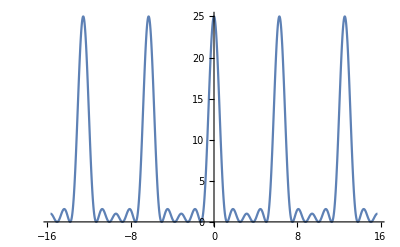

```mathematica
Plot[intensity[5,ϕ],{ϕ,-5Pi, 5Pi},PlotRange->All]
```

```mathematica
derInt[N_,phi_]=Together[D[intensity[N,ϕ],ϕ]]
```

(N sin(N ϕ)+sin(ϕ) cos(N ϕ)-N cos(ϕ) sin(N ϕ)-sin(ϕ))/(cos(ϕ)-1)^2

```mathematica
rts[N_,r_]:=FindRoot[derInt[N,ϕ]==0,{ϕ,r}];
extremum[N_,r_]:=ϕ/.rts[N,r]
```

```mathematica
min8[N_]=extremum[]
```

```mathematica
min8[1]=extremum[8,0.8]
```

0.785398

2.1 Electric Fields

```mathematica
r={x,y,z};r1={x1,y1,z1};
```

```mathematica
r-r1
```

{x-x1,y-y1,z-z1}

```mathematica
(r-r1).(r-r1)
```

(x-x1)^2+(y-y1)^2+(z-z1)^2

```mathematica
EField1[r_,r1_,q1_]=(q1/((r-r1).(r-r1))^(3/2))(r-r1)
```

{(q1 (x-x1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))}

```mathematica
EField1[r,r1,q1]
```

{(q1 (x-x1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (y-y1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(q1 (z-z1))/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))}

```mathematica
EField1[{x,y,0},{1,1,0},1]
```

{(x-x1)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(y-y1)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2)),(z-z1)/(((x-x1)^2+(y-y1)^2+(z-z1)^2)^(3/2))}

```mathematica
{E2D1x,E2D1y}=Take[EField1[{x,y,0},{1,1,0},1],2];
```

```mathematica
VectorPlot[{E2D1x,E2D1y},{x,0,2},{y,0,2},Axes->True]
```

-Graphics-